```mathematica
SetDirectory[NotebookDirectory[]];
<<RISC`HolonomicFunctions`
<<"ZonalPolynomials.m";
```

HolonomicFunctions Package version 1.7.3 (21-Mar-2017)
written by Christoph Koutschan
Copyright Research Institute for Symbolic Computation (RISC),
Johannes Kepler University, Linz, Austria

--> Type  ?HolonomicFunctions  for help.

## Calculate zonal polynomials

When we only give a partition, we obtain the zonal polynomial in terms of the symmetric monomial functions:

```mathematica
ZonalPolynomial[{3,2}]
```

48/7 M[3,2]+176/21 M[2,2,1]+32/7 M[3,1,1]+64/7 M[2,1,1,1]+80/7 M[1,1,1,1,1]

Alternatively, one can give a list of variables as second argument to see the polynomial explicitly:

```mathematica
ZonalPolynomial[{2,1},{a,b,c}]
```

(18 a b c)/5+12/5 (a^2 b+a b^2+a^2 c+b^2 c+a c^2+b c^2)

The coefficients c_(κ,λ) of the zonal polynomials are computed recursively, by the following command:

```mathematica
ZonalCoefficient[{2,1},{1,1,1}]
```

18/5

Let’s compute a zonal coefficient for larger partitions:

```mathematica
ZonalCoefficient[{8,6,6,3},{7,7,5,3,1}]//Timing
```

{4.60311,33426505728/5}

We can create a table of all zonal polynomial coefficients indexed by partitions of n=4:

```mathematica
With[{p=IntegerPartitions[4]},Outer[ZonalCoefficient,p,p,1]]//TableForm
```

1 | 4/7 | 18/35 | 12/35 | 8/35
0 | 24/7 | 16/7 | 88/21 | 32/7
0 | 0 | 16/5 | 32/15 | 16/5
0 | 0 | 0 | 16/3 | 64/5
0 | 0 | 0 | 0 | 16/5

For a simpler (and slightly faster) way to create this table, there is the following command:

```mathematica
ZonalCoefficientTable[4]//TableForm
```

1 | 4/7 | 18/35 | 12/35 | 8/35
0 | 24/7 | 16/7 | 88/21 | 32/7
0 | 0 | 16/5 | 32/15 | 16/5
0 | 0 | 0 | 16/3 | 64/5
0 | 0 | 0 | 0 | 16/5

For the zonal coefficients c_(κ,λ) in the upper left corner, we can derive general closed forms for arbitrary n. This refers to the situation when κ and λ are of the form (n-i,π) where π is a partition of i and where n is symbolic. Here n is assumed to be sufficiently large, so that n-i is greater than or equal to the largest part of π).

```mathematica
ZonalCoefficientN[{n-3,2,1},{n-4,2,2}]
```

(4 (-3+n) (-1+n) n (39-18 n+2 n^2))/(5 (-11+2 n) (-7+2 n))

This is the table that appears in the paper:

```mathematica
part=Flatten[Table[Prepend[#,n-i]&/@IntegerPartitions[i],{i,0,3}],1];
tab=Outer[ZonalCoefficientN,part,part,1];
trad=TraditionalForm/@part;
TableForm[Join[{Prepend[trad,"κ\λ"],{}},Join[Transpose[{trad}],tab,2]]]
```

κ\λ | {n} | {n-1,1} | {n-2,2} | {n-2,1,1} | {n-3,3} | {n-3,2,1} | {n-3,1,1,1}
 |  |  |  |  |  |  | 
{n} | 1 | n/(-1+2 n) | (3 (-1+n) n)/(2 (-3+2 n) (-1+2 n)) | ((-1+n) n)/((-3+2 n) (-1+2 n)) | (5 (-2+n) (-1+n) n)/(2 (-5+2 n) (-3+2 n) (-1+2 n)) | (3 (-2+n) (-1+n) n)/(2 (-5+2 n) (-3+2 n) (-1+2 n)) | ((-2+n) (-1+n) n)/((-5+2 n) (-3+2 n) (-1+2 n))
{n-1,1} | 0 | (2 (-1+n) n)/(-1+2 n) | (2 (-2+n) (-1+n) n)/((-5+2 n) (-1+2 n)) | (2 n (3-6 n+2 n^2))/((-5+2 n) (-1+2 n)) | (3 (-3+n) (-2+n) (-1+n) n)/((-7+2 n) (-5+2 n) (-1+2 n)) | ((-2+n) n (11-20 n+5 n^2))/((-7+2 n) (-5+2 n) (-1+2 n)) | (6 (-2+n) n (2-4 n+n^2))/((-7+2 n) (-5+2 n) (-1+2 n))
{n-2,2} | 0 | 0 | (2 (-3+n) (-2+n) (-1+n) n)/((-5+2 n) (-3+2 n)) | (4 (-3+n) (-2+n) (-1+n) n)/(3 (-5+2 n) (-3+2 n)) | (2 (-4+n) (-3+n) (-2+n) (-1+n) n)/((-9+2 n) (-5+2 n) (-3+2 n)) | (2 (-3+n) (-1+n) n (36-30 n+5 n^2))/(3 (-9+2 n) (-5+2 n) (-3+2 n)) | (4 (-3+n) (-1+n) n (7-6 n+n^2))/((-9+2 n) (-5+2 n) (-3+2 n))
{n-2,1,1} | 0 | 0 | 0 | 2/3 (-2+n) n | 0 | (2 (-3+n) (-2+n) n)/(3 (-7+2 n)) | (2 (-2+n) n (8-9 n+2 n^2))/((-7+2 n) (-3+2 n))
{n-3,3} | 0 | 0 | 0 | 0 | (4 (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n)/(3 (-9+2 n) (-7+2 n) (-5+2 n)) | (4 (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n)/(5 (-9+2 n) (-7+2 n) (-5+2 n)) | (8 (-5+n) (-4+n) (-3+n) (-2+n) (-1+n) n)/(15 (-9+2 n) (-7+2 n) (-5+2 n))
{n-3,2,1} | 0 | 0 | 0 | 0 | 0 | (4 (-4+n) (-3+n) (-1+n) n)/(5 (-7+2 n)) | (6 (-4+n) (-3+n) (-1+n) n)/(5 (-7+2 n))
{n-3,1,1,1} | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-3+n) (-2+n) (-1+n) n)/(3 (-3+2 n))

## Experimentally verify definition with Wishart distribution

Mathematica provides a command for sampling random matrices according to the Wishart distribution.
Here we show the distribution of the largest eigenvalue of a 2*2 Wishart matrix with parameter ν = 3.

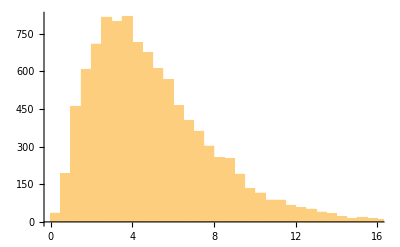

```mathematica
Histogram[Table[Max[Eigenvalues[RandomVariate[WishartMatrixDistribution[3,IdentityMatrix[2]]]]],{10000}]]
```

However, it is also possible (and easy) to define the Wishart distribution in terms of the normal distribution:

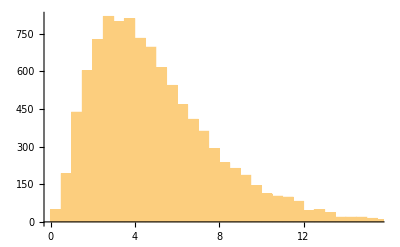

```mathematica
Histogram[Table[Max[Eigenvalues[With[{X=Table[RandomVariate[NormalDistribution[0,1]],{3},{2}]},Transpose[X].X]]],{10000}]]
```

```mathematica
(* Symmetric functions U_lambda. They form a basis. *)
SymU[λ_,y_]:=If[Length[λ]>Length[y],0,With[{lam=Append[λ,0]},Product[SymmetricPolynomial[i,y]^(lam[[i]]-lam[[i+1]]),{i,Length[λ]}]]];
BasisU[n_,y_]:=DeleteCases[SymU[#,y]&/@IntegerPartitions[n],0];
BasisU[3,{y1,y2}]
```

{(y1+y2)^3,y1 y2 (y1+y2)}

```mathematica
(* The result of the map tau, when we use only a single randomly generated matrix. *)
τ[ν_,U_]:=
Module[{y=Variables[U],W,ev},
W=RandomVariate[WishartMatrixDistribution[ν,IdentityMatrix[Length[y]]]];
W=Round[W*10^6]/10^6;
ev=Eigenvalues[DiagonalMatrix[y].W];
Return[N[Expand[U/.Thread[y->ev]]]];
];
τ[3,SymU[{3,1},{y1,y2}]]
```

57.9262 y1^3 y2+125.688 y1^2 y2^2+68.1796 y1 y2^3

```mathematica
(* Compare exact result and Monte-Carlo simulation for two variables. *)
Test2[n_,ν_,s_:10000]:=
Module[{parts,matXi,Lam,eqns,sim},
parts=Select[IntegerPartitions[n],Length[#]≤2&];
matXi=Table[xi[i,j],{i,Length[parts]},{j,Length[parts]}];
eqns=matXi.BasisU[n,{y1,y2}]-(With[{k=Length[#]},Product[(2*#[[i]]+k-i)!,{i,k}]*(2n)!/(2^n*n!*Product[2*#[[i]]-2*#[[j]]-i+j,{i,k-1},{j,i+1,k}])]*ZonalPolynomial[#,{y1,y2}]&)/@parts;
matXi=matXi/.First[Solve[Thread[Flatten[CoefficientList[#,{y1,y2}]&/@eqns]==0],Flatten[matXi]]];
Lam=DiagonalMatrix[2^n*Product[Pochhammer[(ν+1-i)/2,#[[i]]],{i,Length[#]}]&/@parts];
Print["Exact: ",Expand[Inverse[matXi].Lam.matXi.BasisU[n,{y1,y2}]]];
Print["Simul: ",sim=Expand[Sum[τ[ν,BasisU[n,{y1,y2}]],{s}]/s]];
Return[sim];
]
```

```mathematica
Test2[2,2];
```

Exact: {8 y1^2+8 y1 y2+8 y2^2,2 y1 y2}

Simul: {7.92291 y1^2+7.88879 y1 y2+8.00125 y2^2,1.94553 y1 y2}

```mathematica
Test2[2,5];
```

Exact: {35 y1^2+50 y1 y2+35 y2^2,20 y1 y2}

Simul: {34.4961 y1^2+49.2853 y1 y2+35.1559 y2^2,19.6292 y1 y2}

```mathematica
Test2[3,4];
```

Exact: {192 y1^3+288 y1^2 y2+288 y1 y2^2+192 y2^3,72 y1^2 y2+72 y1 y2^2}

Simul: {186.481 y1^3+286.749 y1^2 y2+292.3 y1 y2^2+198.762 y2^3,72.533 y1^2 y2+73.5663 y1 y2^2}

```mathematica
Timing[Test2[4,3,10^5];]
```

Exact: {945 y1^4+1260 y1^3 y2+1350 y1^2 y2^2+1260 y1 y2^3+945 y2^4,210 y1^3 y2+300 y1^2 y2^2+210 y1 y2^3,120 y1^2 y2^2}

Simul: {972.691 y1^4+1271.69 y1^3 y2+1350.69 y1^2 y2^2+1255.93 y1 y2^3+926.755 y2^4,212.809 y1^3 y2+302.703 y1^2 y2^2+211.776 y1 y2^3,121.414 y1^2 y2^2}

{745.62,Null}

## Zonal polynomials are the eigenfunctions of the Laplace-Beltrami operator

We do an experimental verification that the zonal polynomials are the eigenfunctions of the Laplace-Beltrami operator.

```mathematica
LaplaceBeltrami[{x,y,z}]
```

x^2 D_x^2+y^2 D_y^2+z^2 D_z^2+(x^2/(x-y)+x^2/(x-z))D_x+(y^2/(-x+y)+y^2/(y-z))D_y+(z^2/(-x+z)+z^2/(-y+z))D_z

```mathematica
Table[
With[{y=Array[x,n]},
Function[λ,Together[
ApplyOreOperator[LaplaceBeltrami[y],ZonalPolynomial[λ,y]]/
((ρ[λ]+(Length[y]-1)*Total[λ])*ZonalPolynomial[λ,y])
]]/@Select[Join@@Table[IntegerPartitions[n],{n,2,10}],Length[#]≤Length[y]&]
],{n,5}]
```

{{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

## Proofs

### Proof of Proposition 6.2

```mathematica
fj=(b-2j)/d/(2b-2d+1)*Binomial[b,j]*Pochhammer[1/2,j]/Pochhammer[b-j+1/2,j]
```

((b-2 j) Binomial[b,j] Pochhammer[1/2,j])/((1+2 b-2 d) d Pochhammer[1/2+b-j,j])

```mathematica
ct=Factor[CreativeTelescoping[fj,S[j]-1,{S[b],S[d]}]]
```

{{1},{-((1+2 b-2 j) j)/(b-2 j)}}

```mathematica
gj=Simplify[ApplyOreOperator[-ct[[2,1]],fj]]
```

((1+2 b-2 j) j Binomial[b,j] Pochhammer[1/2,j])/((1+2 b-2 d) d Pochhammer[1/2+b-j,j])

```mathematica
(* Sanity check: verify the identity g(j+1)-g(j)=f(j) *)
FullSimplify[((gj/.j->j+1)-gj)/fj]
```

1

```mathematica
gj/.{{j->0},{j->d}}
```

{0,(Binomial[b,d] Pochhammer[1/2,d])/Pochhammer[1/2+b-d,d]}

### Proof of Theorem 6.3

```mathematica
(* closed form given in Theorem 6.3 *)
cf[a_,b_,d_]:=Binomial[b,d]*(b+1/2)*(2a-b)!/(a-b)!/b!*Pochhammer[1/2,d]/Pochhammer[b-d+1/2,a-b+d+1];
cf[a_,b_,d_]:=(b+1/2)*(2a-b)!*Pochhammer[1/2,d]/d!/(b-d)!/(a-b)!/Pochhammer[b-d+1/2,a-b+d+1];
cf[a,b,d]
```

((1/2+b) (2 a-b)! Pochhammer[1/2,d])/((a-b)! (b-d)! d! Pochhammer[1/2+b-d,1+a-b+d])

```mathematica
Clear[ff]
SetDelayed@@{ff[a_,b_,d_],Simplify[cf[a+d,b+2d,d]]/((2a-b)!/a!/(a-b)!)}
ff[a,b,d]
```

((1+2 b+4 d) a! (a-b)! Pochhammer[1/2,d])/(2 (a-b-d)! d! (b+d)! Pochhammer[1/2+b+d,1+a-b])

```mathematica
ct=CreativeTelescoping[ff[a,b,d],S[d]-1,{S[b],S[a]}]//Factor
```

{{S_a-1,S_b-1},{(2 d (b+d))/((1+a-b-d) (1+2 b+4 d)),-(d (1+2 a+2 d))/((a-b) (1+2 b+4 d))}}

```mathematica
g1=ApplyOreOperator[-ct[[2,1]],ff[a,b,d]]
g2=ApplyOreOperator[-ct[[2,2]],ff[a,b,d]]
```

-((d (b+d) a! (a-b)! Pochhammer[1/2,d])/((1+a-b-d) (a-b-d)! d! (b+d)! Pochhammer[1/2+b+d,1+a-b]))

(d (1+2 a+2 d) a! (a-b)! Pochhammer[1/2,d])/(2 (a-b) (a-b-d)! d! (b+d)! Pochhammer[1/2+b+d,1+a-b])

```mathematica
(* Some manual simplifications on the g's (formulas from the paper) *)
Clear[g1,g2];
g1[d_]:=-((a! (a-b)! Pochhammer[1/2,d])/((d-1)! (b+d-1)!(a-b-d+1)! Pochhammer[1/2+b+d,1+a-b]));
g2[d_]:=(a! (a-b-1)! Pochhammer[1/2,d])/((d-1)! (b+d)!(a-b-d)! Pochhammer[1/2+b+d,a-b]);
(* Sanity check: verify identities (6.6) and (6.7). *)
FullSimplify[(ff[a+1,b,d]-ff[a,b,d])/(g1[d+1]-g1[d])]
FullSimplify[(ff[a,b+1,d]-ff[a,b,d])/(g2[d+1]-g2[d])]
```

1

1

```mathematica
g1[a-b+1]-g1[0]+ff[a+1,b,a-b+1]
```

-Pochhammer[1/2,1+a-b]/Pochhammer[3/2+a,1+a-b]+((1+4 (1+a-b)+2 b) Pochhammer[1/2,1+a-b])/(2 Pochhammer[3/2+a,2+a-b])

```mathematica
Together[%/.Pochhammer[3/2+a,a-b+2]->(5/2+2a-b)*Pochhammer[3/2+a,a-b+1]]
```

0

```mathematica
g2[a-b+1]-g2[0]-ff[a,b+1,a-b]
```

0